#### 1)

```mathematica
f=1/x^2+2 √x;
g=ArcTan[x]/Log[x];
h=x^3 Tan[x^2];
D[f,x]
D[g,x]
D[h,x]
```

-2/x^3+1/(√x)

-ArcTan[x]/(x Log[x]^2)+1/((1+x^2) Log[x])

2 x^4 Sec[x^2]^2+3 x^2 Tan[x^2]

#### 2)

48 x-24 x^2-4 x^3+3 x^4

48-48 x-12 x^2+12 x^3

{{x→-2},{x→1},{x→2}}

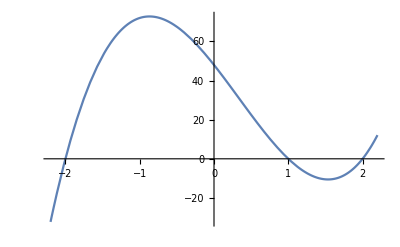

3 x^4-4 x^3-24 x^2+48 x

```mathematica
(x-1)(x+2)(x-2)//Expand;
Integrate[%,x]12//Expand
%//TeXForm
D[%,x]
Solve[%==0,x]
Plot[%%,{x,-2.2,2.2}]
```

#### 3)

```mathematica
1/(2+3I)-I/(3-2I)
(z+2-5I)(z+2+5I)//Expand
Solve[29+4 z+z^2==0,z]
```

4/13-(6 ⅈ)/13

29+4 z+z^2

{{z→-2-5 ⅈ},{z→-2+5 ⅈ}}

#### 4)

```mathematica
1/(x+3)+3/(x-2)//Together
Numerator[%]/Expand[Denominator[%]]
Integrate[%,x]
%%//TeXForm
```

(7+4 x)/((-2+x) (3+x))

(7+4 x)/(-6+x+x^2)

3 Log[2-x]+Log[3+x]

\frac{4 x+7}{x^2+x-6}

#### 5)

{{x→-1},{x→2}}

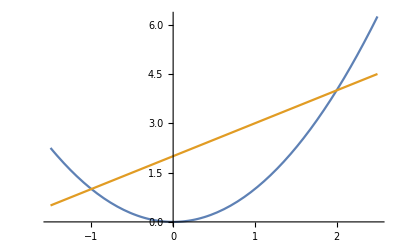

9/2

```mathematica
y1=x^2;
y2=x+2;
Solve[y1==y2,x]
Plot[{y1,y2},{x,-1.5,2.5}]
Integrate[y2-y1,{x,-1,2}]
```

#### 6)

```mathematica
A1={{1,2,3},{2,1,-1},{-3,2,3}}
X1={{1},{2},{-1}};
B1=A1.X1
Solve[A1.{{x},{y},{z}}==B1,{x,y,z}]
Det[A1]
```

{{1,2,3},{2,1,-1},{-3,2,3}}

{{2},{5},{-2}}

{{x→1,y→2,z→-1}}

20